r-2 x

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

{√(4 h+r^2),-√(4 h+r^2)}

{{x→r/2}}

{{h→-r^2/4}}

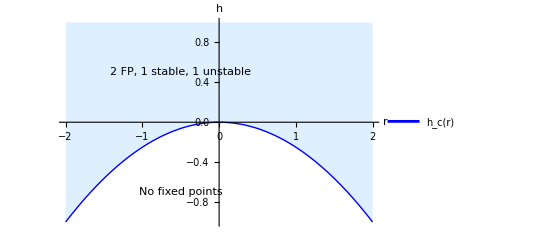

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];

f[x_,h_,r_]:=h+x*(r-x);
fPrime=D[f[x,h,r],x]

(*Solutions, the positive one is unstable, the negative one is stable"*)
(*For h < h_c(r) we dont have any real roots, and thus no fixed points in this case*)
fixedPoints=Solve[f[x,h,r]==0,x]
stability=fPrime/. x -> x/. fixedPoints 

(*Bifurcation curve *)
xSolution = Solve[fPrime == 0,x]
hSolution[r_]= Solve[f[x/.xSolution,h,r] == 0,h]

Plot[
{h /. hSolution[r]},{r,-2,2},
PlotRange->{{-2,2},{-1,1}},
Filling->{1->{1,LightBlue}},
AxesLabel->{"r","h"},
PlotStyle->{Blue,Thick},
LabelStyle->{FontSize->14},Epilog->{Text["2 FP, 1 stable, 1 unstable",{-0.5,0.5},{1,0}],Text["No fixed points",{-0.5,-0.7},{1,0}]},
PlotLegends->{"h_c(r)"}
]
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
f[x_,h_,r_]:=h+x* (r-x)

fixedPoints=Solve[f[x,h,r]==0,x]

fixedPointPos=x/. fixedPoints[[1]]; (*Unstable*)
fixedPointNeg=x/. fixedPoints[[2]]; (*Stable*)

Plot3D[
Evaluate[{fixedPointPos,fixedPointNeg}],{r,-2,2},{h,-1,1},
PlotRange->All,
AxesLabel->{"r","h","x*"},
PlotLabel->"Fixed Points in (r, h, x*)"]
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

-Graphics3D-